## The Heisenberg Uncertainty Principle

## The Hand-Waving Version

In a typical modern physics course you would just learn that  Δx·Δp≥ℏ/2. In words, you would say that “on the quantum scale, position and momentum cannot be simultaneously determined,” and that “Δx represents the uncertainty in position and Δp represents the uncertainty in momentum.” That would be the end of the statement of the Heisenberg Uncertainty Principle.

## The Heisenberg Uncertainty Principle in Everyday Life

Compared to the uncertainties we encounter in everyday life, ℏ is such a tiny amount of angular momentum — ℏ=6.626 x10^-34 kg·m^2/s — that you never notice that position and momentum cannot be simultaneously determined. 

For example, if you measure the Δx of a particle to one nanometer, and the Δp to 10^-9 kg·m/s — good luck being that accurate with either quantity, let alone both — then the product of those two uncertainties is 10^-18 kg·m^2/s. You would still have almost a 10^16 increase in accuracy to play around with before you hit the fundamental limits of quantum mechanics!

## Rigorously Defining Uncertainty in x

The problem with the hand-waving version is that uncertainty in position and uncertainty in momentum have not been rigorously defined. You went a long way toward defining these in Problem Set 10, but I made a few simplifying assumptions. Now we are going to do the complete version, starting with the uncertainty in x.

Given a normalized wave function ψ(x), we define:

OverBar[x^n]=∫_(-∞)^∞ ψ^*(x)x^n ψ(x)dx=∫_(-∞)^∞ x^n(|ψ(x)|)^2 dx

Physicists often write this as ⟨ψ|x^n|ψ⟩ or just  ⟨x^n⟩ and read it as “the expectation value of x^n.”

As a special case:

x̄=∫_(-∞)^∞ ψ^*(x)xψ(x)dx=∫_(-∞)^∞ x(|ψ(x)|)^2 dx

As another special case (zero powers of x):

b̄=∫_(-∞)^∞ ψ^*(x)bψ(x)dx=b∫_(-∞)^∞ (|ψ(x)|)^2 dx=b·1=b

is true for any number, b, as a consequence of normalization. And as a consequence of this,

OverBar[x̄]=x̄

because x̄ is a number.

To finish the job define

(Δx)^2≡OverBar[(x-x̄)^2]

or if you prefer

Δx≡√OverBar[(x-x̄)^2]

## Rigorously Defining Uncertainty in p

This is going to proceed quite analogously to the uncertainty in x. Given a normalized wave function ψ(x), we define:

(OverBar[p^n]=∫_(-∞)^∞ ψ^*(x) (ℏ/i∂/(∂x)))^n ψ(x)dx

Physicists often write this as ⟨ψ|p^n|ψ⟩ or just  ⟨p^n⟩ and read it as “the expectation value of p^n.”

As a special case:

p̄=∫_(-∞)^∞ ψ^*(x) ℏ/i∂/(∂x)ψ(x)dx

As another special case (zero powers of p):

b̄=∫_(-∞)^∞ ψ^*(x)bψ(x)dx=b∫_(-∞)^∞ (|ψ(x)|)^2 dx=b·1=b

and as a consequence of this,

OverBar[p̄]=p̄

because p̄ is a number.

To finish the job define

(Δp)^2≡OverBar[(p-p̄)^2]

or if you prefer

Δp≡√OverBar[(p-p̄)^2]

## A Restatement of Δx and Δp

You will often see this restatement of the definition of (Δx)^2:

(Δx)^2≡OverBar[x^2]-(x̄)^2

I am not a fan, because it isn’t as obvious what is happening, and furthermore, it is numerically unstable if you ask a computer to use this version, but it follows trivially from (Δx)^2=OverBar[(x-x̄)^2]. The proof is:

OverBar[(x-x̄)^2]=OverBar[x^2-2x x̄+(x̄)^2]=OverBar[x^2]-2 x̄ x̄+(x̄)^2=OverBar[x^2]-(x̄)^2

 and there are times when one or the other version is the more convenient one.

As a special case, if x̄ is zero, then

(Δx)^2=OverBar[x^2]

Similarly you will often see

(Δp)^2≡OverBar[p^2]-(p̄)^2

and that follows with the same trivial and yet somehow deep proof from  (Δp)^2=OverBar[(p-p̄)^2].

As a special case, if p̄ is zero, then

(Δp)^2=OverBar[p^2]

In Problem Set 10, we were using those special cases some of the time. Now you are liberated by having the full, rigorous definitions!!

## Precisely Stating the Principle

Finally we can precisely state the Heisenberg Uncertainty Principle, and the statement is, exactly as in the naive statement,

 Δx·Δp≥ℏ/2

but now you know what the quantities precisely mean.

## An Important Example

The “Gaussian” is the most important example of the Heisenberg Uncertainty Principle. (I think) that it can be proved as the only function for which equality holds:

 Δx·Δp=ℏ/2.

Ask Ryan. He deals with proofs involving Fourier transforms all the time. Heck, I ought to be able to prove it too, but I don’t want to get more sidetracked than I already am as part of this class and handout.

Here is what I mean by a “Gaussian” in this context:

ψ(x)=N e^(i p_0 x / ℏ)e^(-(x-x_0)^2/2 a^2)

In most contexts, people mean that a “Gaussian” is the absolute square of this,

(|ψ(x)|)^2=N^2 e^(-(x-x_0)^2/a^2)

and even more commonly, x_0 is taken to be zero, leaving just:

(|ψ(x)|)^2=N^2 e^(-x^2/a^2)

In Problem Set 10, you often used that normalization requires

N^2=1/(√π a)

and so the very simplest form of the Gaussian is

(|ψ(x)|)^2=1/(√π a)e^(-x^2/a^2)

## Contact with Statistics

In a statistics course, you will see the Gaussian defined as,

g(x)=1/(√(2π)σ)e^(-(x-μ)^2/2 σ^2)

they call this “the normal distribution,” and μ is the “mean,” and σ is the “standard deviation,” or σ^2 is the “variance.”

Other than the replacements x_0->μ and a^2->2 σ^2 this is the same function as we are working with.

We aren’t statisticians, and we won’t use their notation or results. However, it would not be fair to those of you who have had AP Statistics to skip over this bit of contact. With the statisticians’ notation, if x is σ away from μ (e.g., x=μ-σ or x=μ+σ), then

g(x)=1/(√(2π)σ)e^(-σ^2/2 σ^2)=1/(√(2π)σ)e^(-1/2)

We can have Mathematica plot an example with a mean of 5 and a standard deviation of 2,

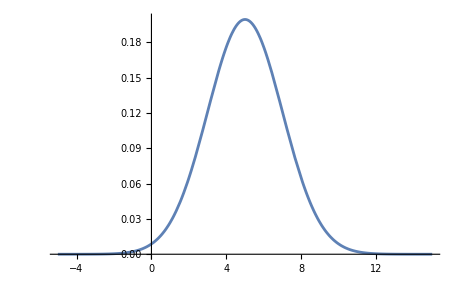

```mathematica
μ=5; σ=2;Plot[1/(√(2π)σ)Exp[-(x-μ)^2/(2 σ^2)],{x,μ-5σ,μ+5σ},PlotRange->{{μ-5σ,μ+5σ},{0,0.2}}]
```

Let’s zoom in on the range from just μ-σ to μ+σ

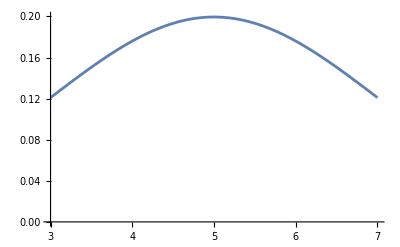

```mathematica
μ=5; σ=2;Plot[1/(√(2π)σ)Exp[-(x-μ)^2/(2 σ^2)],{x,μ-σ,μ+σ},PlotRange->{{μ-σ,μ+σ},{0,0.2}}]
```

We can have Mathematica integrate this function over this range,

```mathematica
μ=5; σ=2;N[Integrate[1/(√(2π)σ)Exp[-(x-μ)^2/(2 σ^2)],{x,μ-σ,μ+σ}]]
```

0.682689

This is the famous result that in a normal distribution 68% of the samples lie within ±1σ of the mean, μ.

Let’s have Mathematica integrate from  x=μ-2σ to x=μ+2σ,

```mathematica
μ=5; σ=2;N[Integrate[1/(√(2π)σ)Exp[-(x-μ)^2/(2 σ^2)],{x,μ-2σ,μ+2σ}]]
```

0.9545

95.5% of the samples lie within ±2σ of the mean! Another famous result.

Let’s have Mathematica integrate from  x=μ-3σ to x=μ+3σ,

```mathematica
μ=5; σ=2;N[Integrate[1/(√(2π)σ)Exp[-(x-μ)^2/(2 σ^2)],{x,μ-3σ,μ+3σ}]]
```

0.9973

99.7% of the samples lie within ±3σ of the mean. Of course, all these famous results presume that the samples are normally distributed, and only in idealized situations is this actually true.

## Returning to The Important Example

Please ignore the technicalities of the previous section if you have never taken AP statistics.  Before we got sidetracked making contact with statistics, we were considering:

ψ(x)=N e^(i p_0 x / ℏ)e^(-(x-x_0)^2/2 a^2)

We need to compute x̄, OverBar[x^2], p̄, OverBar[p^2]. Two of these are easy:

x̄=x_0

and

p̄=p_0

So this example that I have been claiming is important has the very simple interpretation that the expectation value of x is x_0 and the expectation value of p is p_0.

Continuing on with the quantities we are going to need to know to compute  Δx·Δp is one that you pretty much did on the homework:

OverBar[x^2]=x_0^2+1/2 a^2

I’ll just do the last of the four quantities, because it is the messiest. I’ll start with the form you get after parts integration:

 OverBar[p^2]=ℏ^2∫_(-∞)^∞ N^2 (∂/(∂x)e^(-i p_0 x / ℏ -(x-x_0)^2/2 a^2))(∂/(∂x)e^(i p_0 x / ℏ -(x-x_0)^2/2 a^2))dx
=ℏ^2∫_(-∞)^∞ N^2 (-ip_0/ℏ-(x-x_0)/a^2)e^(-i p_0 x / ℏ -(x-x_0)^2/2 a^2)(ip_0/ℏ-(x-x_0)/a^2)e^(i p_0 x / ℏ -(x-x_0)^2/2 a^2)dx
=ℏ^2/a^4∫_(-∞)^∞ N^2 ((-ip_0 a^2)/ℏ-(x-x_0))((ip_0 a^2)/ℏ-(x-x_0))e^(-(x-x_0)^2/a^2)dx
=ℏ^2/a^4∫_(-∞)^∞ N^2 ((p_0^2 a^4)/ℏ^2+(x-x_0)^2)e^(-(x-x_0)^2/a^2)dx
=ℏ^2/a^4∫_(-∞)^∞ N^2 ((p_0^2 a^4)/ℏ^2+(x-x_0)^2)e^(-(x-x_0)^2/a^2)dx
=ℏ^2/a^4(p_0^2 a^4)/ℏ^2+ℏ^2/a^4 1/2 a^2
=p_0^2+1/2 ℏ^2/a^2

## Summarizing the Important Example

We are finally in a position to summarize our calculation of  Δx·Δp for ψ(x)=N e^(i p_0 x / ℏ)e^(-(x-x_0)^2/2 a^2). Putting our  x̄, OverBar[x^2], p̄, OverBar[p^2] values into the definitions of  Δx and  Δp, we discover that this function saturates the inequality in the Heisenberg Uncertainty Principle:

 Δx·Δp=√(OverBar[x^2]-(x̄)^2)√(OverBar[p^2]-(p̄)^2)=√(OverBar[x^2]-x_0^2)√(OverBar[p^2]-p_0^2)=√(1/2 a^2)√(1/2 ℏ^2/a^2)=ℏ/2

I am claiming that this function is important for three reasons:

(1) It represents a particle that is expected to have its position be near x_0. To state it statistically, it has a 68% chance of being within a/(√2) of x_0. To state it in the way of the Heisenberg Uncertainty Principle, Δx=a/(√2).

(2) It represents a particle that is expected have its momentum be near p_0. When we calculated OverBar[p^2], we learned that Δp=√(OverBar[p^2]-p_0^2)=√(1/2 ℏ^2/a^2)=ℏ/(√2 a). I didn’t show that p was normally distributed, but it is plausible, and if so, then it has a 68% chance of being within ℏ/(√2 a) of p_0.

(3) The product of the uncertainty in x and the uncertainty in p is ℏ/2 and I am claiming that no other function does better or even as well in saturating the inequality in the Heisenberg Uncertainty Principle. The more you decrease a and improve the certainty of x, the more you increase the uncertainty in p. Equivalently, the more you increase a and improve the certainty of p, the more you increase the uncertainty in x.

I guess I could give two more reasons the example is important:

(4) This type of function shows up in ordinary, classical statistics.

(5) This type of function is easy to work with because it is the exponential of a quadratic. Ok, it is annoying that it is a complex quadratic, 

ψ(x)∝e^(i p_0 x / ℏ-(x-x_0)^2/2 a^2)

but it was easy to take derivatives of and complex conjugate this function thanks to the simple properties of exponentials, and the easy complex conjugation of complex numbers in polar form.